```mathematica
Quit[]
```

This notebook can be used to find the thermal history of the Universe in the Standard Model. 
This code is based on Escudero 1812.05605 and 2001.XXXXX.

### Basic Instructions

The code works as follows:

1) Evaluate the Basic Modules Section. 
2) Evaluate the Standard Model Section. It takes ~.1d20 s per example evaluation.
3) Evaluate the Standard Model with neutrino chemical potentials Section. It takes ~30 s per example evaluation.

Note that everything is in MeV Units but the rates, the Hubble parameter and time which are in seconds.

### Basic Modules (need to be loaded first)

This Section loads the main common Modules: 
	1) Thermodynamic Formulae 
	2) Finite Temperature QED corrections
	3) SM ν-ν and ν-e Interaction Rates
	4) Constants and Parameters
	
These modules are loaded from BasicModules.m. One can alternatively copy the content of BasicModules.nb here and load it locally.

```mathematica
(* Load Basic Modules *)
SetDirectory[NotebookDirectory[]];
Quiet[<<BasicModules.m];
```

### Standard Model

#### Hubble Parameter and total Energy and Pressure of the Universe

```mathematica
Clear[ρtot,ptot,Hubble,RHSec];
ρtot[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=(2ρBE[Tγ,0]+4 ρFDM[Tγ,0,me]+2ρFD[Tνe,μνe]+4ρFD[Tνμ,μνμ]-Pint[Tγ]+Tγ dPintdT[Tγ]);
ptot[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=(2pBE[Tγ,0]+4 pFDM[Tγ,0,me]+2pFD[Tνe,μνe]+4pFD[Tνμ,μνμ]+Pint[Tγ]);
Hubble[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=((ρtot[Tγ,Tνe,Tνμ,μνe,μνμ]) (8 π)/(3 (Mpl)^2))^(1/2)FacMeVtos1;
RHSec[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=-3 Hubble[Tγ,Tνe,Tνμ,μνe,μνμ](ρtot[Tγ,Tνe,Tνμ,μνe,μνμ]+ ptot[Tγ,Tνe,Tνμ,μνe,μνμ]);
```

#### Temperature ODEs

```mathematica
Clear[dTγdt,dTνdt,dTνedt,dTνμdt];

(* Equation 2.14 of 1812.05605 *)
dTγdt[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=-1/(2 (2 π^2 Tγ^3)/15+4dρdTFDM[Tγ,0,me]+Tγ d2PintdT2[Tγ])( Hubble[Tγ,Tνe,Tνμ,μνe,μνμ] ( 4 2 ρBE[Tγ,0]+3 4*(ρFDM[Tγ,0,me]+pFDM[Tγ,0,me])+3 Tγ dPintdT[Tγ]) + ΔρSMνe[Tγ,Tνe,Tνμ,μνe,μνμ]+2 ΔρSMνμ[Tγ,Tνe,Tνμ,μνe,μνμ]);

(* Equations 2.9 of 1812.05605 *)
dTνdt[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=-Hubble[Tγ,Tνe,Tνμ,μνe,μνμ] Tνe +1/3 (ΔρSMνe[Tγ,Tνe,Tνμ,μνe,μνμ]+2ΔρSMνμ[Tγ,Tνe,Tνμ,μνe,μνμ])/(2dρFDdT[Tνe,μνe]);

dTνedt[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=-Hubble[Tγ,Tνe,Tνμ,μνe,μνμ] Tνe + ΔρSMνe[Tγ,Tνe,Tνμ,μνe,μνμ]/(2dρFDdT[Tνe,μνe]);
dTνμdt[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=-Hubble[Tγ,Tνe,Tνμ,μνe,μνμ] Tνμ + ΔρSMνμ[Tγ,Tνe,Tνμ,μνe,μνμ]/(2dρFDdT[Tνμ,μνμ]);


(* Comoving Variables, zγ = a Tγ/m0, zν = a Tν/m0 *)
(* Using equations 3.10 of 2001.XXXXX  *)

dzγda[zγ_,zνe_,zνμ_,ξνe_,ξνμ_,a_]:=zγ/a(1+dTγdt[(zγ m0)/a,(zνe m0)/a,(zνμ m0)/a,(ξνe zνe m0)/a,(ξνμ zνμ m0)/a]/(Hubble[(zγ m0)/a,(zνe m0)/a,(zνμ m0)/a,(ξνe zνe m0)/a,(ξνμ zνμ m0)/a]((zγ m0)/a)));
dzνda[zγ_,zνe_,zνμ_,ξνe_,ξνμ_,a_]:=zνe/a(1+dTνdt[(zγ m0)/a,(zνe m0)/a,(zνμ m0)/a,(ξνe zνe m0)/a,(ξνμ zνμ m0)/a]/(Hubble[(zγ m0)/a,(zνe m0)/a,(zνμ m0)/a,(ξνe zνe m0)/a,(ξνμ zνμ m0)/a]((zνe m0)/a)));

dzνeda[zγ_,zνe_,zνμ_,ξνe_,ξνμ_,a_]:=zνe/a(1+dTνedt[(zγ m0)/a,(zνe m0)/a,(zνμ m0)/a,(ξνe zνe m0)/a,(ξνμ zνμ m0)/a]/(Hubble[(zγ m0)/a,(zνe m0)/a,(zνμ m0)/a,(ξνe zνe m0)/a,(ξνμ zνμ m0)/a]((zνe m0)/a)));
dzνμda[zγ_,zνe_,zνμ_,ξνe_,ξνμ_,a_]:=zνμ/a(1+dTνμdt[(zγ m0)/a,(zνe m0)/a,(zνμ m0)/a,(ξνe zνe m0)/a,(ξνμ zνμ m0)/a]/(Hubble[(zγ m0)/a,(zνe m0)/a,(zνμ m0)/a,(ξνe zνe m0)/a,(ξνμ zνμ m0)/a]((zνμ m0)/a)));
```

#### Definition of observables

```mathematica
Clear[Nefffunc,gstars,gstar,OmeganuMdiv];

Nefffunc[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=8/7(11/4)^(4/3)(2 ρFD[Tνe,μνe]+4 ρFD[Tνμ,μνμ])/(2ρBE[Tγ,0]);

gstars[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=45/(2 π^2 Tγ^3)(2 sFD[Tνe,μνe]+4sFD[Tνμ,μνμ]+2sBE[Tγ,0]+4sFDM[Tγ,0,me]);
```

```mathematica
gstar[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=30/π^2 ρtot[Tγ,Tνe,Tνμ,μνe,μνμ]/Tγ^4;

OmeganuMdiv[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=(3/2 rhocrit/Tγ00^3 Tγ^3/(nFD[Tνe,μνe]+2nFD[Tνμ,μνμ]))/.{rhocrit-> 8.0992 10^-11 eV^4,Tγ00-> 2.7255 Kel}/.{Kel-> 1/(1.16045 10^4)eV}/.eV-> 1;
```

#### SM Key Functions

```mathematica
(* Function used to solve for neutrino decoupling considering a common neutrino temperature.*)
(* Otputs: Tγ[t], Tν[t], t0, tmax *)
FuncSMnudec[]:=(

Tmax=10.1;    (* Start integration at 10 MeV *)
Tmin=0.009; (* Finish integration at Tγ ~ 0.009. By then all e+e- have annihilated away *)

t0=1/(2 Hubble[Tmax,Tmax,Tmax,0,0]);
tmax=1/(2 Hubble[Tmin,Tmin/1.4,Tmin/1.4,0,0]);
tCPU1=TimeUsed[];
(* Solve the ODE system *)
solEarlyUniverset=NDSolve[{ 
Tγ'[t]==dTγdt[Tγ[t],Tν[t],Tν[t],0,0],
Tν'[t]==dTνdt[Tγ[t],Tν[t],Tν[t],0,0],
Tγ[t0]==Tmax,Tν[t0]==Tmax},{Tγ,Tν},{t,t0,tmax},PrecisionGoal->10,AccuracyGoal->10];

tCPU2=TimeUsed[];
Print["tCPU = ", tCPU2-tCPU1];


Tγoftfunc[t1_]:=(Tγ[t]/.solEarlyUniverset)[[1]]/.{t-> t1};
Tνoftfunc[t1_]:=(Tν[t]/.solEarlyUniverset)[[1]]/.{t-> t1};

{Tγoftfunc[t],Tνoftfunc[t],t0,tmax});


(* Function used to solve for neutrino decoupling considering Tνe ≠ Tνμ. *)
(* Otputs: Tγ[t], Tνe[t], Tνμ[t], t0, tmax *)
FuncSMnudecflav[]:=(

Tmax=10.1;    (* Start integration at 10 MeV *)
Tmin=0.009; (* Finish integration at Tγ ~ 0.009. By then all e+e- have annihilated away *)

t0=1/(2 Hubble[Tmax,Tmax,Tmax,0,0]);
tmax=1/(2 Hubble[Tmin,Tmin/1.4,Tmin/1.4,0,0]);
tCPU1=TimeUsed[];
(* Solve the ODE system *)
solEarlyUniverset=NDSolve[{ 
Tγ'[t]==dTγdt[Tγ[t],Tνe[t],Tνμ[t],0,0],
Tνe'[t]==dTνedt[Tγ[t],Tνe[t],Tνμ[t],0,0],Tνμ'[t]==dTνμdt[Tγ[t],Tνe[t],Tνμ[t],0,0],
Tγ[t0]==Tmax,Tνe[t0]==Tmax,Tνμ[t0]==Tmax},{Tγ,Tνe,Tνμ},{t,t0,tmax},PrecisionGoal->8,AccuracyGoal->8,Method->{"EquationSimplification"->"Residual"}];

tCPU2=TimeUsed[];
Print["tCPU = ", tCPU2-tCPU1];

Tγoftfunc[t1_]:=(Tγ[t]/.solEarlyUniverset)[[1]]/.{t-> t1};
Tνeoftfunc[t1_]:=(Tνe[t]/.solEarlyUniverset)[[1]]/.{t-> t1};
Tνμoftfunc[t1_]:=(Tνμ[t]/.solEarlyUniverset)[[1]]/.{t-> t1};

{Tγoftfunc[t],Tνeoftfunc[t],Tνμoftfunc[t],t0,tmax});

(* Same as FuncSMnudec but solved in terms of comoving variables zγ = a Tγ/m0, zν = a Tν/m0 *)
(* Outputs: zγ[a], zν[a], a0, amax *)
FuncSMnudeccomov[]:=(

Tmax=10.1;   (* Start integration at 20 MeV *)
Tmin=0.009; (* Finish integration at Tγ ~ 0.009. By then all e+e- have annihilated away *)

a0=m0/(1.1*Tmax);
amax=m0/(0.9*Tmin/1.4);

(* Solve the ODE system *)
tCPU1=TimeUsed[];

(* Solve the ODE system *)
solEarlyUniverse=NDSolve[
{ 
zγ'[a]==dzγda[zγ[a],zν[a],zν[a],0,0,a],zν'[a]==dzνda[zγ[a],zν[a],zν[a],0,0,a],
zγ[a0]==1,zν[a0]==1
},
{zγ,zν},
{a,a0,amax},
PrecisionGoal->9,AccuracyGoal->9,Method->{"EquationSimplification"->"Residual"}];

tCPU2=TimeUsed[];
Print["tCPU = ", tCPU2-tCPU1];

zγoftfunc[a1_]:=(zγ[a]/.solEarlyUniverse)[[1]]/.{a-> a1};
zνoftfunc[a1_]:=(zν[a]/.solEarlyUniverse)[[1]]/.{a-> a1};

{zγoftfunc[a],zνoftfunc[a],a0,amax});

(* Solved in terms of comoving variables zγ = a Tγ/m0, zνe = a Tνe/m0, zνμ = a Tνμ/m0 *)
(* Function of the case of Tνe, Tνμ, otputs zγ[a], zνe[a], zνμ[a], a0, amax *)
FuncSMnudecflavcomov[]:=(

Tmax=10.1;   (* Start integration at 20 MeV *)
Tmin=0.009; (* Finish integration at Tγ ~ 0.009. By then all e+e- have annihilated away *)

a0=m0/(1.1*Tmax);
amax=m0/(0.9*Tmin/1.4);
(* Solve the ODE system *)
tCPU1=TimeUsed[];

(* Solve the ODE system *)
solEarlyUniverse=NDSolve[
{ 
zγ'[a]==dzγda[zγ[a],zνe[a],zνμ[a],0,0,a],zνe'[a]==dzνeda[zγ[a],zνe[a],zνμ[a],0,0,a],
zνμ'[a]==dzνμda[zγ[a],zνe[a],zνμ[a],0,0,a],
zγ[a0]==1,zνe[a0]==1,zνμ[a0]==1
},
{zγ,zνe,zνμ},
{a,a0,amax},
PrecisionGoal->9,AccuracyGoal->9,Method->{"EquationSimplification"->"Residual"}];


tCPU2=TimeUsed[];
Print["tCPU = ", tCPU2-tCPU1];

zγoftfunc[a1_]:=(zγ[a]/.solEarlyUniverse)[[1]]/.{a-> a1};
zνeoftfunc[a1_]:=(zνe[a]/.solEarlyUniverse)[[1]]/.{a-> a1};
zνμoftfunc[a1_]:=(zνμ[a]/.solEarlyUniverse)[[1]]/.{a-> a1};

{zγoftfunc[a],zνeoftfunc[a],zνμoftfunc[a],a0,amax});
```

#### SM Example Tνe = Tνμ = Tν

```mathematica
resvec=Quiet[FuncSMnudec[]];
```

tCPU = 18.9693

N_eff     = 3.04483

g_(*s)      = 3.93

g_*      = 3.383

∑m_ν/Ω_ν  = 93.06 eV

T_γ/T_νe   = 1.39583

T_γ/T_νμ   = 1.39583

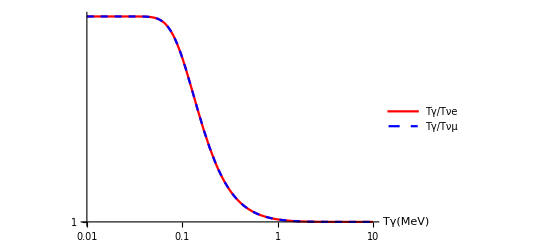

```mathematica
Clear[Tγoft,Tνoft,tofTγ,TγdTνofTγ];
Tγoft[tt_]:=resvec[[1]]/.{t-> tt};
Tνoft[tt_]:=resvec[[2]]/.{t-> tt};
tofTγ[Tgam_]:= InverseFunction[Tγoft][Tgam];
TγdTνofTγ[Tgam_]:=Tgam/Tνoft[tofTγ[Tgam]];

Neffval=Nefffunc[Tγoft[tmax],Tνoft[tmax],Tνoft[tmax],0,0];
gstarval=gstar[Tγoft[tmax],Tνoft[tmax],Tνoft[tmax],0,0];
gstarsval=gstars[Tγoft[tmax],Tνoft[tmax],Tνoft[tmax],0,0];
omeganuval=OmeganuMdiv[Tγoft[tmax],Tνoft[tmax],Tνoft[tmax],0,0];
Tratio=Tγoft[tmax]/Tνoft[tmax];

Print["N_eff     = ", Neffval];
Print["g_(*s)      = ", SetPrecision[gstarsval,4]];
Print["g_*      = ", SetPrecision[gstarval,4]];
Print["∑m_ν/Ω_ν  = ",SetPrecision[omeganuval,4] , " eV"];
Print["T_γ/T_νe   = ", SetPrecision[Tratio,6]];
Print["T_γ/T_νμ   = ", SetPrecision[Tratio,6]];

LogLogPlot[{TγdTνofTγ[Tgam],TγdTνofTγ[Tgam]},{Tgam,10,0.01},PlotLegends->{"Tγ/Tνe","Tγ/Tνμ"},AxesLabel->{"Tγ(MeV)"},PlotStyle->{Red,{Blue,Dashed}}]
```

#### SM Example Tνe != Tνμ

```mathematica
resvec=Quiet[FuncSMnudecflav[]];
```

tCPU = 26.0627

N_eff     = 3.04391

g_(*s)      = 3.93

g_*       = 3.383

∑m_ν/Ω_ν   = 93.08 eV

T_γ/T_νe   = 1.39467

T_γ/T_νμ   = 1.39657

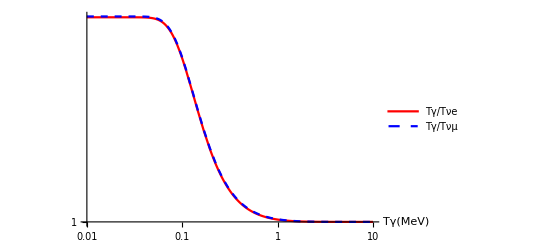

```mathematica
Clear[Tγoft,Tνeoft,Tνμoft,tofTγ,TγdTνeofTγ,TγdTνμofTγ];
Tγoft[tt_]:=resvec[[1]]/.{t-> tt};
Tνeoft[tt_]:=resvec[[2]]/.{t-> tt};
Tνμoft[tt_]:=resvec[[3]]/.{t-> tt};
tofTγ[Tgam_]:= InverseFunction[Tγoft][Tgam];
TγdTνeofTγ[Tgam_]:=Tgam/Tνeoft[tofTγ[Tgam]];
TγdTνμofTγ[Tgam_]:=Tgam/Tνμoft[tofTγ[Tgam]];

Neffval=Nefffunc[Tγoft[tmax],Tνeoft[tmax],Tνμoft[tmax],0,0];
gstarval=gstar[Tγoft[tmax],Tνeoft[tmax],Tνμoft[tmax],0,0];
gstarsval=gstars[Tγoft[tmax],Tνeoft[tmax],Tνμoft[tmax],0,0];
omeganuval=OmeganuMdiv[Tγoft[tmax],Tνeoft[tmax],Tνμoft[tmax],0,0];
Tratioe=Tγoft[tmax]/Tνeoft[tmax];
Tratioμ=Tγoft[tmax]/Tνμoft[tmax];

Print["N_eff     = ", Neffval];
Print["g_(*s)      = ", SetPrecision[gstarsval,4]];
Print["g_*       = ", SetPrecision[gstarval,4]];
Print["∑m_ν/Ω_ν   = ",SetPrecision[omeganuval,4] , " eV"];
Print["T_γ/T_νe   = ", SetPrecision[Tratioe,6]];
Print["T_γ/T_νμ   = ", SetPrecision[Tratioμ,6]];

LogLogPlot[{TγdTνeofTγ[Tgam],TγdTνμofTγ[Tgam]},{Tgam,10,0.01},PlotLegends->{"Tγ/Tνe","Tγ/Tνμ"},AxesLabel->{"Tγ(MeV)"},PlotStyle->{Red,{Blue,Dashed}}]
```

#### SM Example Tνe = Tνμ = Tν, comoving variables

```mathematica
resvec=Quiet[FuncSMnudeccomov[]];
```

tCPU = 10.3545

```mathematica
zγoft[tt_]:=resvec[[1]]/.{a-> tt};
zνoft[tt_]:=resvec[[2]]/.{a-> tt};

Neffval=Nefffunc[zγoft[amax],zνoft[amax],zνoft[amax],0,0];

Print["N_eff     = ", Neffval];
Print["z_γ      = ", SetPrecision[zγoft[amax],6]];
Print["z_ν      = ", SetPrecision[zνoft[amax],6]];
Print["T_γ/T_ν   = ", SetPrecision[zγoft[amax]/zνoft[amax],6]];
```

N_eff     = 3.04483

z_γ      = 1.39788

z_ν      = 1.00147

T_γ/T_ν   = 1.39583

#### SM Example Tνe != Tνμ, comoving variables

```mathematica
resvec=Quiet[FuncSMnudecflavcomov[]];
```

tCPU = 23.2634

```mathematica
zγoft[tt_]:=resvec[[1]]/.{a-> tt};
zνeoft[tt_]:=resvec[[2]]/.{a-> tt};
zνμoft[tt_]:=resvec[[3]]/.{a-> tt};

Neffval=Nefffunc[zγoft[amax],zνeoft[amax],zνμoft[amax],0,0];

Print["N_eff     = ", Neffval];
Print["z_γ      = ", SetPrecision[zγoft[amax],6]];
Print["z_νe      = ", SetPrecision[zνeoft[amax],6]];
Print["z_νμ      = ", SetPrecision[zνμoft[amax],6]];
Print["T_γ/T_νe   = ", SetPrecision[zγoft[amax]/zνeoft[amax],6]];
Print["T_γ/T_νμ   = ", SetPrecision[zγoft[amax]/zνμoft[amax],6]];
```

N_eff     = 3.0439

z_γ      = 1.39793

z_νe      = 1.00234

z_νμ      = 1.00097

T_γ/T_νe   = 1.39467

T_γ/T_νμ   = 1.39658

### Standard Model with neutrino chemical potentials

#### Hubble Parameter and total Energy and Pressure of the Universe

```mathematica
Clear[ρtot,ptot,Hubble,RHSec];
ρtot[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=(2ρBE[Tγ,0]+4 ρFDM[Tγ,0,me]+2ρFD[Tνe,μνe]+4ρFD[Tνμ,μνμ]-Pint[Tγ]+Tγ dPintdT[Tγ]);
ptot[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=(2pBE[Tγ,0]+4 pFDM[Tγ,0,me]+2pFD[Tνe,μνe]+4pFD[Tνμ,μνμ]+Pint[Tγ]);
Hubble[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=((ρtot[Tγ,Tνe,Tνμ,μνe,μνμ]) (8 π)/(3 (Mpl)^2))^(1/2)FacMeVtos1;
RHSec[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=-3 Hubble[Tγ,Tνe,Tνμ,μνe,μνμ](ρtot[Tγ,Tνe,Tνμ,μνe,μνμ]+ ptot[Tγ,Tνe,Tνμ,μνe,μνμ]);
```

#### Temperature ODEs

```mathematica
Clear[dTγdt,dTνdt,dTνedt,dTνμdt,dμνdt,dμνedt,dμνμdt];

(* Equation 3.2 of 2001.XXXXX *)
dTγdt[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=-1/(2 (2 π^2 Tγ^3)/15+4dρdTFDM[Tγ,0,me]+Tγ d2PintdT2[Tγ])( Hubble[Tγ,Tνe,Tνμ,μνe,μνμ] ( 4 2 ρBE[Tγ,0]+3 4*(ρFDM[Tγ,0,me]+pFDM[Tγ,0,me])+3 Tγ dPintdT[Tγ]) + ΔρSMνe[Tγ,Tνe,Tνμ,μνe,μνμ]+2 ΔρSMνμ[Tγ,Tνe,Tνμ,μνe,μνμ]);


(* Equation 2.9a of 2001.XXXXX *)
dTνedt[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=1/(dnFDdμ[Tνe,μνe]dρFDdT[Tνe,μνe]-dnFDdT[Tνe,μνe]dρFDdμ[Tνe,μνe])(- 3 Hubble[Tγ,Tνe,Tνμ,μνe,μνμ] ( (ρFD[Tνe,μνe]+pFD[Tνe,μνe])dnFDdμ[Tνe,μνe]-nFD[Tνe,μνe]dρFDdμ[Tνe,μνe]) +dnFDdμ[Tνe,μνe] 1/2 ΔρSMνe[Tγ,Tνe,Tνμ,μνe,μνμ]-dρFDdμ[Tνe,μνe] 1/2 ΔnSMνe[Tγ,Tνe,Tνμ,μνe,μνμ]);

dTνμdt[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=1/(dnFDdμ[Tνμ,μνμ]dρFDdT[Tνμ,μνμ]-dnFDdT[Tνμ,μνμ]dρFDdμ[Tνμ,μνμ])(- 3 Hubble[Tγ,Tνe,Tνμ,μνe,μνμ] ( (ρFD[Tνμ,μνμ]+pFD[Tνμ,μνμ])dnFDdμ[Tνμ,μνμ]-nFD[Tνμ,μνμ]dρFDdμ[Tνμ,μνμ]) +dnFDdμ[Tνμ,μνμ] 1/2 ΔρSMνμ[Tγ,Tνe,Tνμ,μνe,μνμ]-dρFDdμ[Tνμ,μνμ] 1/2 ΔnSMνμ[Tγ,Tνe,Tνμ,μνe,μνμ]);

dTνdt[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=1/(dnFDdμ[Tνe,μνe]dρFDdT[Tνe,μνe]-dnFDdT[Tνe,μνe]dρFDdμ[Tνe,μνe])(- 3 Hubble[Tγ,Tνe,Tνμ,μνe,μνμ] ( (ρFD[Tνe,μνe]+pFD[Tνe,μνe])dnFDdμ[Tνe,μνe]-nFD[Tνe,μνe]dρFDdμ[Tνe,μνe]) +dnFDdμ[Tνe,μνe] 1/2(1/3(ΔρSMνe[Tγ,Tνe,Tνμ,μνe,μνμ]+2ΔρSMνμ[Tγ,Tνe,Tνμ,μνe,μνμ]))-dρFDdμ[Tνe,μνe] 1/2(1/3(ΔnSMνe[Tγ,Tνe,Tνμ,μνe,μνμ]+2ΔnSMνμ[Tγ,Tνe,Tνμ,μνe,μνμ])));

(*The factor of 1/2 accounts for the fact that we are considering a single neutrino species, not the neutrino + antineutrino *)

(* Equation 2.9b of 2001.XXXXX *)
dμνdt[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=-1/(dnFDdμ[Tνe,μνe]dρFDdT[Tνe,μνe]-dnFDdT[Tνe,μνe]dρFDdμ[Tνe,μνe])(- 3 Hubble[Tγ,Tνe,Tνμ,μνe,μνμ] ((ρFD[Tνe,μνe]+pFD[Tνe,μνe])dnFDdT[Tνe,μνe]-nFD[Tνe,μνe]dρFDdT[Tνe,μνe]) +dnFDdT[Tνe,μνe] 1/2(1/3(ΔρSMνe[Tγ,Tνe,Tνμ,μνe,μνμ]+2ΔρSMνμ[Tγ,Tνe,Tνμ,μνe,μνμ]))-dρFDdT[Tνe,μνe] 1/2(1/3(ΔnSMνe[Tγ,Tνe,Tνμ,μνe,μνμ]+2ΔnSMνμ[Tγ,Tνe,Tνμ,μνe,μνμ])));

dμνedt[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=-1/(dnFDdμ[Tνe,μνe]dρFDdT[Tνe,μνe]-dnFDdT[Tνe,μνe]dρFDdμ[Tνe,μνe])(- 3 Hubble[Tγ,Tνe,Tνμ,μνe,μνμ] ((ρFD[Tνe,μνe]+pFD[Tνe,μνe])dnFDdT[Tνe,μνe]-nFD[Tνe,μνe]dρFDdT[Tνe,μνe]) +dnFDdT[Tνe,μνe] 1/2(1/3(ΔρSMνe[Tγ,Tνe,Tνμ,μνe,μνμ]+2ΔρSMνμ[Tγ,Tνe,Tνμ,μνe,μνμ]))-dρFDdT[Tνe,μνe] 1/2(1/3(ΔnSMνe[Tγ,Tνe,Tνμ,μνe,μνμ]+2ΔnSMνμ[Tγ,Tνe,Tνμ,μνe,μνμ])));

dμνμdt[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=-1/(dnFDdμ[Tνμ,μνμ]dρFDdT[Tνμ,μνμ]-dnFDdT[Tνμ,μνμ]dρFDdμ[Tνμ,μνμ])(- 3 Hubble[Tγ,Tνe,Tνμ,μνe,μνμ] ((ρFD[Tνμ,μνμ]+pFD[Tνμ,μνμ])dnFDdT[Tνμ,μνμ]-nFD[Tνμ,μνμ]dρFDdT[Tνμ,μνμ]) +dnFDdT[Tνμ,μνμ] 1/2(1/3(ΔρSMνe[Tγ,Tνe,Tνμ,μνe,μνμ]+2ΔρSMνμ[Tγ,Tνe,Tνμ,μνe,μνμ]))-dρFDdT[Tνμ,μνμ] 1/2(1/3(ΔnSMνe[Tγ,Tνe,Tνμ,μνe,μνμ]+2ΔnSMνμ[Tγ,Tνe,Tνμ,μνe,μνμ])));
```

#### Definition of observables

```mathematica
Clear[Nefffunc,gstars,gstar,OmeganuMdiv];

Nefffunc[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=8/7(11/4)^(4/3)(2 ρFD[Tνe,μνe]+4 ρFD[Tνμ,μνμ])/(2ρBE[Tγ,0]);

gstars[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=45/(2 π^2 Tγ^3)(2 sFD[Tνe,μνe]+4sFD[Tνμ,μνμ]+2sBE[Tγ,0]+4sFDM[Tγ,0,me]);
```

```mathematica
gstar[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=30/π^2 ρtot[Tγ,Tνe,Tνμ,μνe,μνμ]/Tγ^4;

OmeganuMdiv[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=(3/2 rhocrit/Tγ00^3 Tγ^3/(nFD[Tνe,μνe]+2nFD[Tνμ,μνμ]))/.{rhocrit-> 8.0992 10^-11 eV^4,Tγ00-> 2.7255 Kel}/.{Kel-> 1/(1.16045 10^4)eV}/.eV-> 1;
```

#### SM with chemical potentials: Key Functions

```mathematica
(* Function used to solve for neutrino decoupling considering a common Tν and μν .*)
(* Otputs: Tγ[t], Tν[t], μν[t], t0, tmax *)
FuncSMnudecchem[]:=(

Tmax=10.1;    (* Start integration at 10 MeV *)
Tmin=0.009; (* Finish integration at Tγ ~ 0.009. By then e+e- have annihilated away *)

t0=1/(2 Hubble[Tmax,Tmax,Tmax,0,0]);
tmax=1/(2 Hubble[Tmin,Tmin/1.4,Tmin/1.4,0,0]);
tCPU1=TimeUsed[];
(* Solve the ODE system *)
solEarlyUniverset=NDSolve[{ 
Tγ'[t]==dTγdt[Tγ[t],Tν[t],Tν[t],μν[t],μν[t]],
Tν'[t]==dTνdt[Tγ[t],Tν[t],Tν[t],μν[t],μν[t]],
μν'[t]==dμνdt[Tγ[t],Tν[t],Tν[t],μν[t],μν[t]],
Tγ[t0]==Tmax,Tν[t0]==Tmax,μν[t0]== -Tmax 10^-4},{Tγ,Tν,μν},{t,t0,tmax},PrecisionGoal->8,AccuracyGoal->8,Method->{"EquationSimplification"->"Residual"}];
tCPU2=TimeUsed[];
Print["tCPU = ", tCPU2-tCPU1];

Tγoftfunc[t1_]:=(Tγ[t]/.solEarlyUniverset)[[1]]/.{t-> t1};
Tνoftfunc[t1_]:=(Tν[t]/.solEarlyUniverset)[[1]]/.{t-> t1};
μνoftfunc[t1_]:=(μν[t]/.solEarlyUniverset)[[1]]/.{t-> t1};

{Tγoftfunc[t],Tνoftfunc[t],μνoftfunc[t],t0,tmax});


(* Function used to solve for neutrino decoupling considering Tνe, Tνμ, μνe, μνμ .*)
(* Otputs: Tγ[t], Tνe[t], Tνμ[t], μνe[t], μνμ[t], t0, tmax *)
FuncSMnudecflavchem[]:=(

Tmax=10.1;    (* Start integration at 10 MeV *)
Tmin=0.009; (* Finish integration at Tγ ~ 0.009. By then e+e- have annihilated away *)

t0=1/(2 Hubble[Tmax,Tmax,Tmax,0,0]);
tmax=1/(2 Hubble[Tmin,Tmin/1.4,Tmin/1.4,0,0]);

tCPU1=TimeUsed[];
(* Solve the ODE system *)
solEarlyUniverset=NDSolve[{ 
Tγ'[t]==dTγdt[Tγ[t],Tνe[t],Tνμ[t],μνe[t],μνμ[t]],
Tνe'[t]==dTνedt[Tγ[t],Tνe[t],Tνμ[t],μνe[t],μνμ[t]],Tνμ'[t]==dTνμdt[Tγ[t],Tνe[t],Tνμ[t],μνe[t],μνμ[t]],
μνe'[t]==dμνedt[Tγ[t],Tνe[t],Tνμ[t],μνe[t],μνμ[t]],μνμ'[t]==dμνμdt[Tγ[t],Tνe[t],Tνμ[t],μνe[t],μνμ[t]],
Tγ[t0]==Tmax,Tνe[t0]==Tmax,Tνμ[t0]==Tmax,μνe[t0]==- 10^-4 Tmax,μνμ[t0]==- 10^-4 Tmax},{Tγ,Tνe,Tνμ,μνe,μνμ},{t,t0,tmax},PrecisionGoal->8,AccuracyGoal->8,Method->{"EquationSimplification"->"Residual"}];
tCPU2=TimeUsed[];
Print["tCPU = ", tCPU2-tCPU1];

Tγoftfunc[t1_]:=(Tγ[t]/.solEarlyUniverset)[[1]]/.{t-> t1};
Tνeoftfunc[t1_]:=(Tνe[t]/.solEarlyUniverset)[[1]]/.{t-> t1};
Tνμoftfunc[t1_]:=(Tνμ[t]/.solEarlyUniverset)[[1]]/.{t-> t1};
μνeoftfunc[t1_]:=(μνe[t]/.solEarlyUniverset)[[1]]/.{t-> t1};
μνμoftfunc[t1_]:=(μνμ[t]/.solEarlyUniverset)[[1]]/.{t-> t1};

{Tγoftfunc[t],Tνeoftfunc[t],Tνμoftfunc[t],μνeoftfunc[t],μνμoftfunc[t],t0,tmax});
```

#### SM Example Tνe = Tνμ = Tν, μνe = μνμ = μν

```mathematica
resvec=Quiet[FuncSMnudecchem[]];
```

tCPU = 29.6068

N_eff     = 3.04426

g_(*s)      = 3.93

g_*      = 3.383

∑m_ν/Ω_ν  = 93.15 eV

T_γ/T_νe   = 1.39451

T_γ/T_νμ   = 1.39451

T_νe/μ_νe  = -239.3

T_νμ/μ_νμ  = -239.3

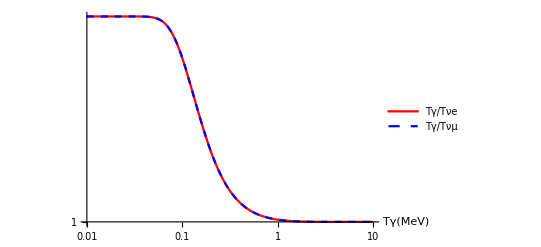

```mathematica
Clear[Tγoft,Tνoft,tofTγ,TγdTνofTγ];
Tγoft[tt_]:=resvec[[1]]/.{t-> tt};
Tνoft[tt_]:=resvec[[2]]/.{t-> tt};
μνoft[tt_]:=resvec[[3]]/.{t-> tt};
tofTγ[Tgam_]:= InverseFunction[Tγoft][Tgam];
TγdTνofTγ[Tgam_]:=Tgam/Tνoft[tofTγ[Tgam]];

Neffval=Nefffunc[Tγoft[tmax],Tνoft[tmax],Tνoft[tmax],μνoft[tmax],μνoft[tmax]];
gstarval=gstar[Tγoft[tmax],Tνoft[tmax],Tνoft[tmax],μνoft[tmax],μνoft[tmax]];
gstarsval=gstars[Tγoft[tmax],Tνoft[tmax],Tνoft[tmax],μνoft[tmax],μνoft[tmax]];
omeganuval=OmeganuMdiv[Tγoft[tmax],Tνoft[tmax],Tνoft[tmax],μνoft[tmax],μνoft[tmax]];
Tratio=Tγoft[tmax]/Tνoft[tmax];
μratio=Tνoft[tmax]/μνoft[tmax];

Print["N_eff     = ", Neffval];
Print["g_(*s)      = ", SetPrecision[gstarsval,4]];
Print["g_*      = ", SetPrecision[gstarval,4]];
Print["∑m_ν/Ω_ν  = ",SetPrecision[omeganuval,4] , " eV"];
Print["T_γ/T_νe   = ", SetPrecision[Tratio,6]];
Print["T_γ/T_νμ   = ",SetPrecision[Tratio,6] ];
Print["T_νe/μ_νe  = ", SetPrecision[μratio,4]];
Print["T_νμ/μ_νμ  = ", SetPrecision[μratio,4]];

LogLogPlot[{TγdTνofTγ[Tgam],TγdTνofTγ[Tgam]},{Tgam,10,0.01},PlotLegends->{"Tγ/Tνe","Tγ/Tνμ"},AxesLabel->{"Tγ(MeV)"},PlotStyle->{Red,{Blue,Dashed}}]
```

#### SM Example Tνe != Tνμ , μνe != μνμ

```mathematica
resvec=Quiet[FuncSMnudecflavchem[]];
```

tCPU = 34.2353

N_eff     = 3.04322

g_(*s)      = 3.93

g_*       = 3.382

∑m_ν/Ω_ν   = 93.17 eV

T_γ/T_νe   = 1.39271

T_γ/T_νμ   = 1.39566

T_νe/μ_νe  = -247.6

T_νμ/μ_νμ  = -245.9

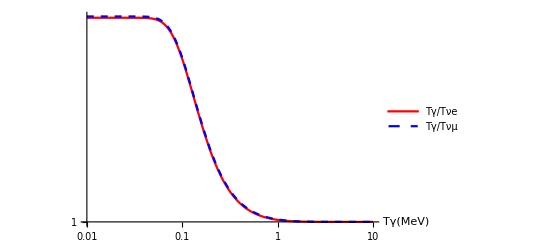

```mathematica
Clear[Tγoft,Tνeoft,Tνμoft,μνeoft,μνμoft,tofTγ,TγdTνeofTγ,TγdTνμofTγ];
Tγoft[tt_]:=resvec[[1]]/.{t-> tt};
Tνeoft[tt_]:=resvec[[2]]/.{t-> tt};
Tνμoft[tt_]:=resvec[[3]]/.{t-> tt};
μνeoft[tt_]:=resvec[[4]]/.{t-> tt};
μνμoft[tt_]:=resvec[[5]]/.{t-> tt};
tofTγ[Tgam_]:= InverseFunction[Tγoft][Tgam];
TγdTνeofTγ[Tgam_]:=Tgam/Tνeoft[tofTγ[Tgam]];
TγdTνμofTγ[Tgam_]:=Tgam/Tνμoft[tofTγ[Tgam]];

Neffval=Nefffunc[Tγoft[tmax],Tνeoft[tmax],Tνμoft[tmax],μνeoft[tmax],μνμoft[tmax]];
gstarval=gstar[Tγoft[tmax],Tνeoft[tmax],Tνμoft[tmax],μνeoft[tmax],μνμoft[tmax]];
gstarsval=gstars[Tγoft[tmax],Tνeoft[tmax],Tνμoft[tmax],μνeoft[tmax],μνμoft[tmax]];
omeganuval=OmeganuMdiv[Tγoft[tmax],Tνeoft[tmax],Tνμoft[tmax],μνeoft[tmax],μνμoft[tmax]];
Tratioe=Tγoft[tmax]/Tνeoft[tmax];
Tratioμ=Tγoft[tmax]/Tνμoft[tmax];
μratioe=Tνeoft[tmax]/μνeoft[tmax];
μratioμ=Tνμoft[tmax]/μνμoft[tmax];

Print["N_eff     = ", Neffval];
Print["g_(*s)      = ", SetPrecision[gstarsval,4]];
Print["g_*       = ", SetPrecision[gstarval,4]];
Print["∑m_ν/Ω_ν   = ",SetPrecision[omeganuval,4] , " eV"];
Print["T_γ/T_νe   = ", SetPrecision[ Tratioe,6]];
Print["T_γ/T_νμ   = ", SetPrecision[ Tratioμ,6]];
Print["T_νe/μ_νe  = ",SetPrecision[ μratioe,4]];
Print["T_νμ/μ_νμ  = ", SetPrecision[μratioμ,4]];
LogLogPlot[{TγdTνeofTγ[Tgam],TγdTνμofTγ[Tgam]},{Tgam,10,0.01},PlotLegends->{"Tγ/Tνe","Tγ/Tνμ"},AxesLabel->{"Tγ(MeV)"},PlotStyle->{Red,{Blue,Dashed}}]
```